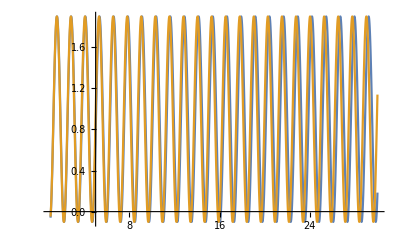

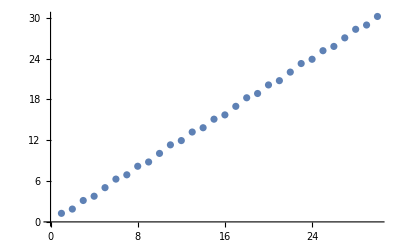

```mathematica
(*Ensure frequency extraction is accurate for straightforward sines*)
DataLength=10.;
SamplingRate=0.01;
XVals=Range[0,DataLength,SamplingRate];
TryGetFreq[truefreq_,offset_]:=(
data=Sin[truefreq*XVals]+offset;
data-=Mean@data;
PowerSpec=Abs[Fourier[Normalize@data]];
PowerPeaks=FindPeaks[Take[PowerSpec,Round[DataLength/(SamplingRate*2)]]];
PeakIndex=TakeLargestBy[PowerPeaks,Last,1]⟦1,1⟧;

Return[(2^-0.5*PeakIndex-2^-0.5)*0.89]
)
OutFreqs=Table[TryGetFreq[x],{x,1,30}];
outfreqp2=TryGetFreq[5,0.9];
Plot[{Sin[5x]+0.9,Sin[outfreqp2 x]+0.9},{x,1,30}]
ListPlot[OutFreqs]
```